### Mathematica to solve Friedmann equations

Friedmann equations (w/ c =1):

H^2 = [da]^2/a^2 =  (8πG)/3 ρ - k/a^2 + Λ/3

(d^2 a)/a = (-4πG)/3(ρ + 3P)

Parameters:

k deals with curvature; k = 1 for sphere/ closed, k=0 flat universe, k=-1 for open universe/hyperbolic space

Λ: cosmological constant/ dark energy

m: matter energy density ~ m/a^3

C: radiation energy density ~ C/a^4

G: Newton’s gravitational constant G = 6.67408*10^-11

Goal is to solve the Friedmann equations for a(t), the radius of universe, at time t

Cases 1-3 double check against Dr. McGuigan

```mathematica
ClearAll
```

ClearAll

## Case 1: Dark energy and curvature

Case given by Dr. McGuigan
Parameter values: k = 1,  Λ = 3,  8πG = c = 1,  ρ(matter) = 0

1. Solve for t as an integral over a

```mathematica
∫((Λ a^2)/3-k )^(-1/2)ⅆa
```

(√3 ArcTanh[(a √Λ)/(√(-3+a^2 Λ))])/(√Λ)

2. Full simplify to get in better form

```mathematica
FullSimplify[-1/2 Log[1-a/(√(-1+a^2))]+1/2 Log[1+a/(√(-1+a^2))]]
```

ArcTanh[a/(√(-1+a^2))]

3.  Invert to solve for a(t)

```mathematica
Solve[t == (√3 ArcTanh[(a √Λ)/(√(-3+a^2 Λ))])/(√Λ), a]
```

{{a→-(√3 Tanh[(t √Λ)/(√3)])/(√(-Λ+Λ Tanh[(t √Λ)/(√3)]^2))},{a→(√3 Tanh[(t √Λ)/(√3)])/(√(-Λ+Λ Tanh[(t √Λ)/(√3)]^2))}}

```mathematica
Plot[(√3 Tanh[t ])/(√(-√3+√3 Tanh[t ]^2)), {t, 0, 100},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}]
```

-Graphics-

No plot for above (????), but the above answer reduces to Cosh[t]

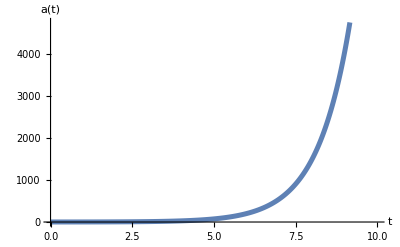

```mathematica
Plot[Cosh[t], {t,0,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}]
```

Plot shows a(t) increasing exponentially at large t, corresponding to an accelerating universe

## Case 2: Dark energy and radiation

Case given by Dr McGuigan
Parameter values: k = 0,  Λ = 0.1,  C = 1, m = 0

```mathematica
Clear[Λ]
```

```mathematica
∫(Λ/3 a^2+1/a^2)^(-1/2)ⅆa
```

(√(3+a^4 Λ) ArcSinh[(a^2 √Λ)/(√3)])/(2 a √Λ √(1/a^2+(a^2 Λ)/3))

```mathematica
Solve[t == (√(3+a^4 Λ) ArcSinh[(a^2 √Λ)/(√3)])/(2 a √Λ √(1/a^2+(a^2 Λ)/3)), a]
```

{{a→-(3^(1/4) √Sinh[(2 t √Λ)/(√3)])/Λ^(1/4)},{a→(3^(1/4) √Sinh[(2 t √Λ)/(√3)])/Λ^(1/4)}}

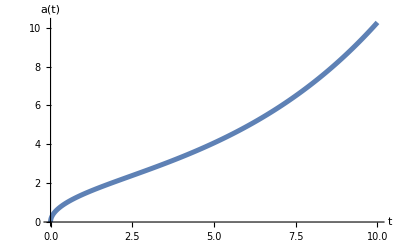

```mathematica
Plot[(3^(1/4) √Sinh[(2 t √0.1)/(√3)])/(0.1)^(1/4), {t,0,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}]
```

## Case 3: Matter & Dark Energy (ΛCDM)

Case given by Dr McGuigan
Parameter values: k = 0,  Λ = 0.1,  C = 0, m = 1

```mathematica
∫(Λ/3 a^2+1/(3a))^(-1/2)ⅆa
```

(2 √(1+a^3 Λ) ArcSinh[a^(3/2) √Λ])/(√3 √a √Λ √(1/a+a^2 Λ))

```mathematica
Solve[t == (2 √(3+a^3 Λ) ArcSinh[(a^(3/2) √Λ)/(√3)])/(3 √a √Λ √(1/a+(a^2 Λ)/3)), a]
```

{{a→-((-3)^(1/3) Sinh[1/2 √3 t √Λ]^(2/3))/Λ^(1/3)},{a→(3^(1/3) Sinh[1/2 √3 t √Λ]^(2/3))/Λ^(1/3)},{a→((-1)^(2/3) 3^(1/3) Sinh[1/2 √3 t √Λ]^(2/3))/Λ^(1/3)}}

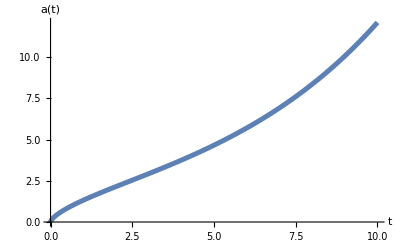

```mathematica
Plot[(3^(1/3) Sinh[1/2 √3 t √0.1]^(2/3))/(0.1)^(1/3),{t,0,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}]
```

## Case 4: Realistic parameters/ Benchmark Model (ΛCDM)

Like model given by Dr. McGuigan (Case #3)  
k = 0, C = 0,  Λ = 0.73 , m = 0.27  (baryonic matter = 0.04 & dark matter = 0.23)
corresponds to flat universe mostly compromised by dark energy and matter (energy density for radiation very low )

```mathematica
∫(Λ/3 a^2+m/(3a))^(-1/2)ⅆa
```

(2 √(m+a^3 Λ) ArcTanh[(a^(3/2) √Λ)/(√(m+a^3 Λ))])/(√3 √a √Λ √((m+a^3 Λ)/a))

```mathematica
FullSimplify[(2 √(m+a^3 Λ) ArcTanh[(a^(3/2) √Λ)/(√(m+a^3 Λ))])/(√3 √a √Λ √((m+a^3 Λ)/a))]
```

(2 √a √((m+a^3 Λ)/a) ArcTanh[(a^(3/2) √Λ)/(√(m+a^3 Λ))])/(√3 √Λ √(m+a^3 Λ))

```mathematica
Solve[t == (2 √a √((m+a^3 Λ)/a) ArcTanh[(a^(3/2) √Λ)/(√(m+a^3 Λ))])/(√3 √Λ √(m+a^3 Λ)), a]
```

{{a→(m^(1/3) Tanh[1/2 √3 t √Λ]^(2/3))/((Λ-Λ Tanh[1/2 √3 t √Λ]^2)^(1/3))},{a→-((-1)^(1/3) m^(1/3) Tanh[1/2 √3 t √Λ]^(2/3))/((Λ-Λ Tanh[1/2 √3 t √Λ]^2)^(1/3))},{a→((-1)^(2/3) m^(1/3) Tanh[1/2 √3 t √Λ]^(2/3))/((Λ-Λ Tanh[1/2 √3 t √Λ]^2)^(1/3))}}

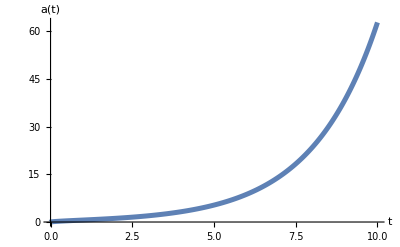

```mathematica
Plot[((0.27)^(1/3) Tanh[1/2 √3 t √0.73]^(2/3))/((0.73-0.73 Tanh[1/2 √3 t √0.73]^2)^(1/3)),{t,0,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}]
```

Exponentially expanding universe

## Case 5: Other ΛCDM models

Try 3 cases:
1.  k = 0, C = 0,  Λ =  , m = 
2.  k = 0, C = 0,  Λ =  , m = 
3.  k = 0, C = 0,  Λ =  , m =

## Case 6: Einstein-de Sitter

Matter only, flat universe with flat spatial dimension , no dark energy (cosmological constant)
Parameter values: k = 0,  Λ = 0,  C = 0, manipulate m between 0.1 and 4 (usually seen with m =1)

```mathematica
∫(m/(3a))^(-1/2)ⅆa
```

(2 a)/(√3 √(m/a))

```mathematica
Solve[t ==  (2 a)/(√3 √(m/a)), a]
```

{{a→-((-3)^(1/3) m^(1/3) t^(2/3))/2^(2/3)},{a→(3^(1/3) m^(1/3) t^(2/3))/2^(2/3)},{a→((-1)^(2/3) 3^(1/3) m^(1/3) t^(2/3))/2^(2/3)}}

```mathematica
Manipulate[Plot[(3^(1/3) matter^(1/3) *t^(2/3))/2^(2/3), {t,0,100}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}], {matter, .1, 4}]
```

## Case 7: Friedmann-Einstein

Parameter values: k = 0,  Λ = 0,  C = 0, manipulate m between 0.1 and 0.5

## Case 8: de Sitter

Flat universe with dark energy only
Parameter values: vary Λ between 0.01-1, k = 0,  C = 0, m = 0

```mathematica
∫(Λ/3 a^2)^(-1/2)ⅆa
```

(√3 a Log[a])/(√(a^2 Λ))

```mathematica
Solve[t == (√3 a Log[a])/(√(a^2 Λ)), a]
```

{{a→ⅇ^((t √Λ)/(√3))}}

```mathematica
Manipulate[Plot[ⅇ^((t √Λ)/(√3)), {t,0,100}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}], {Λ, 0.01, 1}]
```

Rapidly accelerating universe

## Case 9: Milne Universe

Empty universe with curvature
Parameter values: ρ = C = Λ = 0, k must be a negative number (choose -1)

```mathematica
Clear[k]
```

```mathematica
∫(k)^(-1/2)ⅆa
```

a/(√k)

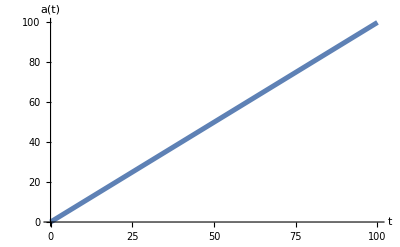

```mathematica
Plot[√1 t,  {t,0,100}, BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"t","a(t)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}]
```

Expands linearly - makes sense

## Case 10: Matter with closed curvature

k = -1, m =1

```mathematica
∫(m/(3a) - k)^(-1/2)ⅆa
```

-(a √(-k+m/(3 a)))/k-(m ArcTan[(√(-k+m/(3 a)))/(√k)])/(3 k^(3/2))

```mathematica
Simplify[-(a √(-k+m/(3 a)))/k-(m ArcTan[(√(-k+m/(3 a)))/(√k)])/(3 k^(3/2))]
```

-(a √(-k+m/(3 a)))/k-(m ArcTan[(√(-k+m/(3 a)))/(√k)])/(3 k^(3/2))

```mathematica
Solve[t == -(a √(-1+1/(3 a)))/1-(m ArcTan[(√(-1+1/(3 a)))/(√1)])/(3 1^(3/2)), a ]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[t==-√(-1+1/(3 a)) a-1/3 m ArcTan[√(-1+1/(3 a))],a]

*** Cannot solve this way, try NdSolve way that Dr McGuigan sent, with m =1 and k = -1***

```mathematica
ode1={a'[t]-√((1/(3*a[t]))+ 1)==0,a[0]==1};
```

```mathematica
sol=NDSolve[ode1,a,{t,0,10}]
```

{{a→InterpolatingFunction[…]}}

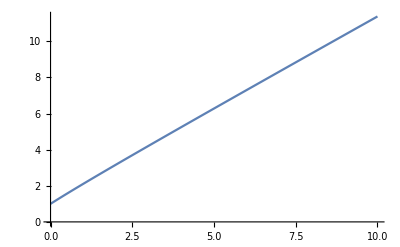

```mathematica
Plot[a[t]/.sol,{t,0,10}]
```

*** With m = 6, k = -5 ***

```mathematica
ode2={a'[t]+√((6/(3*a[t]))+ 5)==0,a[0]==1};
sol2=NDSolve[ode2,a,{t,0,10}]
```

{{a→InterpolatingFunction[…]}}

Having a hard time getting results that show closed universe

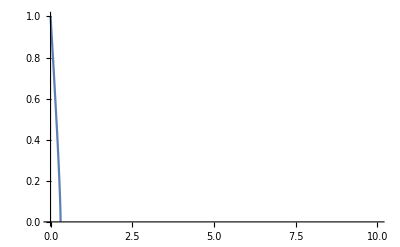

```mathematica
Plot[a[t]/.sol2,{t,0,10}]
```

## Case : Negative cosmological constant

Look at McGuigan paper mentioned